# Practical 8

### Submitted By- Puranjyoti Bera (20201043)

Find a parameterization of the polynomial of the polygon path C = C_1+ C_2+ C_3 from -1 + i to 3 - i where C_1 is the line from -1 + i to -1, C_2 is the line from -1 to 1 + i and C_3 is the line from 1 + i to 3 - i. Make a plot of this path.

The parameterizations of C_1, C_2 and C_3 are given by

C_1:z_1(t)=(-1+ⅈ) (1-t)-t , 0⩽t⩽1

C_1:z_2(t)=-1+(2+ⅈ) t , 0⩽t⩽1

C_1:z_3(t)=(1+ⅈ) (1-t)+(3-ⅈ) t , 0⩽t⩽1

The path of the polygonal path C is given by the figure

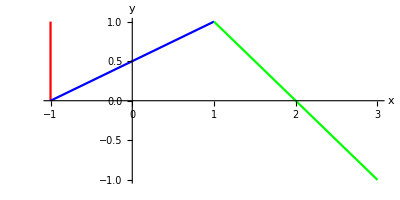

```mathematica
w1:=-1+I;
w2:=-1;
w3:=1+I;
w4:=3-I;
z1[t_]:=(1-t)*w1+t*w2;
z2[t_]:=(1-t)*w2+t*w3;
z3[t_]:=(1-t)*w3+t*w4;
Print["The parameterizations of C_1, C_2 and C_3 are given by"];
Print["C_1:z_1(t)=",z1[t]," , 0⩽t⩽1"];
Print["C_1:z_2(t)=",z2[t]," , 0⩽t⩽1"];
Print["C_1:z_3(t)=",z3[t]," , 0⩽t⩽1"];
Print["The path of the polygonal path C is given by the figure"]
ParametricPlot[{{Re[z1[t]],Im[z1[t]]},{Re[z2[t]],Im[z2[t]]},{Re[z3[t]],Im[z3[t]]}},{t,0,1},PlotStyle-> {Red,Blue,Green},AxesLabel->{x,y}]
```